# Vandermonde Matrix

By Manuel A. Diaz, NTU, 2012.07.10

```mathematica
Quit[]; (* to reset Mathematica kernel *)
```

#### Change Notebook Background

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[0.1,0.1,0.1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[170/255,240/255,140/255]]
```

#### Set Notebook background back to default

```mathematica
SetOptions[EvaluationNotebook[],Background->RGBColor[1,1,1]]
```

```mathematica
SetOptions[EvaluationNotebook[],FontColor->RGBColor[0,0,0]]
```

## Interpolation Tools

### The Mathematica Tools

Let’s assume we with to interpolate the following data

```mathematica
𝓍 = {-2,-1,1,2}; 𝓎 = {10,4,6,3};
```

let’s orginize this information into xy points,

```mathematica
n = Length[𝓍];
```

```mathematica
points=Table[{𝓍[[i]],𝓎[[i]]},{i,n}]
```

{{-2,10},{-1,4},{1,6},{2,3}}

Now, let use our favorite interpolation tools in Mathematica:

The interpolation function

```mathematica
f = Interpolation[points]
```

InterpolatingFunction[{{-2,2}},<>]

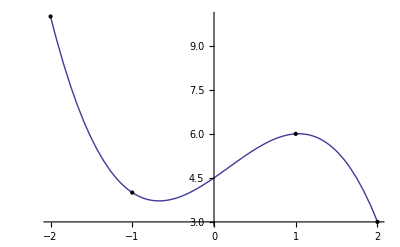

```mathematica
Plot[f[x], {x,-2,2}, Epilog->Map[Point, points]]
```

Interpolation Polynomial

```mathematica
p =InterpolatingPolynomial[points,x]
```

10+(2+x) (-6+(7/3-11/12 (-1+x)) (1+x))

```mathematica
Expand[p]
```

9/2+(23 x)/12+x^2/2-(11 x^3)/12

```mathematica
Show[Plot[p,{x,-2,2}],Epilog->Map[Point, points]]
```

-Graphics-

Therefore Interpolation Polynomail is our best tool for the job!

### The Vandermonde Matrix, why?

Our interpolation is of the form:

```mathematica
Clear[P]
```

```mathematica
p = Plus@@Table[Subscript[a, i] x^i,{i,0,n}]
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4

```mathematica
A= Table[p/.x-> 𝓍[[i]],{i,1,n}]; A//TableForm
```

a_0-2 a_1+4 a_2-8 a_3+16 a_4
a_0-a_1+a_2-a_3+a_4
a_0+a_1+a_2+a_3+a_4
a_0+2 a_1+4 a_2+8 a_3+16 a_4

Thus, the Vandermonde Matrix of our system is,

```mathematica
V= Transpose[Table[Coefficient[A,Subscript[a, i]],{i,0,n-1}]];V//MatrixForm
```

(1 | -2 | 4 | -8
1 | -1 | 1 | -1
1 | 1 | 1 | 1
1 | 2 | 4 | 8)

with vectors of coeficients and interpolated data

```mathematica
coef = Table[Subscript[a, i],{i,n}]
```

{a_1,a_2,a_3,a_4}

```mathematica
𝓎
```

{10,4,6,3}

Let us solve this system:  V.a == 𝓎

```mathematica
{Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4]} = LinearSolve[V,𝓎]
```

{9/2,23/12,1/2,-11/12}

This is the same result from the Interpolation polynomial.

### The Legendre Vandermonde Matrix

What is so special about this matrix?
To understand what it does let us build a simple case: use ξ_n Lobatto (LGL) points, and P_(n-1) Legendre polynomials for i = 1...6,

```mathematica
normalizedLegendre = Orthogonalize[{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},Integrate[#1 #2,{x,-1,1}]&] //Expand;
```

```mathematica
normalizedLegendre[[9]]
```

(35 √(17/2))/128-315/32 √(17/2) x^2+3465/64 √(17/2) x^4-3003/32 √(17/2) x^6+6435/128 √(17/2) x^8

```mathematica
legendreP =Table[LegendreP[i,x],{i,0,8}]; Table[Subscript[p, i]=legendreP[[i+1]],{i,0,8}]; lobatto = Table[Subscript[p, k]-Subscript[p, k-2],{k,2,7}] //Simplify;Table[Subscript[Lo, i]= lobatto[[i]],{i,1,6}]; abscissas= -Sort[List @@ Roots[Subscript[Lo, 6]==0,x][[All,2]],Greater]; {Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4],Subscript[ξ, 5],Subscript[ξ, 6],Subscript[ξ, 7]} =N[abscissas];
```

```mathematica
legendreP
```

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5),1/16 (-5+105 x^2-315 x^4+231 x^6),1/16 (-35 x+315 x^3-693 x^5+429 x^7),1/128 (35-1260 x^2+6930 x^4-12012 x^6+6435 x^8)}

```mathematica
abscissas
```

{-1,-√(1/33 (15+2 √15)),-√(1/33 (15-2 √15)),0,√(1/33 (15-2 √15)),√(1/33 (15+2 √15)),1}

Legendre Vandermonde

```mathematica
V =  Table[LegendreP[j-1,Subscript[ξ, i]],{i,1,7},{j,1,7}]; V//N//MatrixForm
```

(1. | -1. | 1. | -1. | 1. | -1. | 1.
1. | -0.830224 | 0.533908 | -0.185289 | -0.131226 | 0.344336 | -0.41475
1. | -0.468849 | -0.170271 | 0.445618 | -0.23792 | -0.155707 | 0.332106
1. | 0. | -0.5 | 0. | 0.375 | 0. | -0.3125
1. | 0.468849 | -0.170271 | -0.445618 | -0.23792 | 0.155707 | 0.332106
1. | 0.830224 | 0.533908 | 0.185289 | -0.131226 | -0.344336 | -0.41475
1. | 1. | 1. | 1. | 1. | 1. | 1.)

Normalized Legendre Vandermonde

```mathematica
Vnormal =  Table[normalizedLegendre[[j]]/.x->Subscript[ξ, i],{i,1,7},{j,1,7}]; Vnormal//N//MatrixForm
```

(0.707107 | -1.22474 | 1.58114 | -1.87083 | 2.12132 | -2.34521 | 2.54951
0.707107 | -1.01681 | 0.844182 | -0.346644 | -0.278373 | 0.807539 | -1.05741
0.707107 | -0.57422 | -0.269222 | 0.833675 | -0.504704 | -0.365166 | 0.846707
0.707107 | 0. | -0.790569 | 0. | 0.795495 | 0. | -0.796722
0.707107 | 0.57422 | -0.269222 | -0.833675 | -0.504704 | 0.365166 | 0.846707
0.707107 | 1.01681 | 0.844182 | 0.346644 | -0.278373 | -0.807539 | -1.05741
0.707107 | 1.22474 | 1.58114 | 1.87083 | 2.12132 | 2.34521 | 2.54951)

Which is in great agreement example (d) in the table of Figure 3.1. See Hesthaven and Warburton’s reference.

#### Lets explore a more simple escenario from FEM

choose i = 1,2,3

```mathematica
abscissas= -Sort[List @@ Roots[Subscript[Lo, 3]==0,x][[All,2]],Greater]; {Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]} =abscissas; abscissas
```

{-1,-1/(√5),1/(√5),1}

```mathematica
V =  Table[LegendreP[j-1,Subscript[ξ, i]],{i,1,4},{j,1,4}]; V//MatrixForm
```

(1 | -1 | 1 | -1
1 | -1/(√5) | -1/5 | 1/(√5)
1 | 1/(√5) | -1/5 | -1/(√5)
1 | 1 | 1 | 1)

```mathematica
Vnormal =  Table[normalizedLegendre[[j]]/.x->Subscript[ξ, i],{i,1,4},{j,1,4}]; Vnormal//MatrixForm
```

(1/(√2) | -√(3/2) | √(5/2) | -√(7/2)
1/(√2) | -√(3/10) | -(√(5/2))/2+3/(2 √10) | √(7/10)
1/(√2) | √(3/10) | -(√(5/2))/2+3/(2 √10) | -√(7/10)
1/(√2) | √(3/2) | √(5/2) | √(7/2))

from FEM we have the base functions are defined by the relation [M] {Ne(x)} = {P(x)}, where

```mathematica
P[x_]:= ({{1}, {x}, {x^2}, {x^3}}) (* Monomial Basis *)
```

if we define M as,

```mathematica
M = Table[Subscript[ξ, j]^i,{j,1,4},{i,0,3}]; M//MatrixForm
```

(1 | -1 | 1 | -1
1 | -1/(√5) | 1/5 | -1/(5 √5)
1 | 1/(√5) | 1/5 | 1/(5 √5)
1 | 1 | 1 | 1)

I always performed this:

```mathematica
Ne[x_]:= Transpose[Inverse[M]].P[x]
```

so that my shape functions (lagrange polynomials) are,

```mathematica
Ne[ξ]//Expand
```

{{-1/8+ξ/8+(5 ξ^2)/8-(5 ξ^3)/8},{5/8-(5 √5 ξ)/8-(5 ξ^2)/8+(5 √5 ξ^3)/8},{5/8+(5 √5 ξ)/8-(5 ξ^2)/8-(5 √5 ξ^3)/8},{-1/8-ξ/8+(5 ξ^2)/8+(5 ξ^3)/8}}

As expected this polynomials exhibit a δ_ij property,

```mathematica
Table[Ne[Subscript[ξ, i]],{i,4}]//MatrixForm
```

((1) | (0) | (0) | (0)
(0) | (1) | (0) | (0)
(0) | (0) | (1) | (0)
(0) | (0) | (0) | (1))

```mathematica
P[Subscript[ξ, 2]]
```

{{1},{-1/(√5)},{1/5},{-1/(5 √5)}}

```mathematica
Transpose[M].Ne[Subscript[ξ, 2]]
```

{{1},{-1/(√5)},{1/5},{-1/(5 √5)}}

### Now for the conclusion this afternoon’s experiment

So for our (normal) Legendre Vandermonde Matrix we have

```mathematica
Transpose[{Table[LegendreP[2,Subscript[ξ, i]],{i,1,4}] }]//MatrixForm
```

(1
-1/5
-1/5
1)

Is it the same value?

```mathematica
V.Ne[Subscript[ξ, 2]]//MatrixForm
```

(-1
-1/(√5)
1/(√5)
1)

```mathematica
Transpose[{Table[LegendreP[j-1,Subscript[ξ, 2]],{j,1,4}]}] //MatrixForm
```

(1
-1/(√5)
-1/5
1/(√5))

```mathematica
Transpose[Vnormal].Ne[Subscript[ξ, i]]==Transpose[{Table[normalizedLegendre[[j]]/.x->Subscript[ξ, i],{j,1,4}]}] /.i->3
```

True

Yes! we get all the Legendre and normal legendre P_n evaluated at the same point ξ_i

### Thus we conclude (V_ij)^ᵀ. ϕ(ξ_i) = P_(j-1)(ξ_i) pass!